#### A two-host, environmental-transmission model

This model assumes environmental transmission, but where the parasite actively seeks out hosts. Contact is thus controlled by the parasite (so β_i can quantify both the contact and infection processes), and contact is assumed to remove parasites from the environment. I will assume that the resident parasite strain exploits a single host and ask whether a mutant that can exploit both hosts can invade if “generalism” comes at a cost of reducing the shedding rate from both hosts. Let the parameter a quantify the cost of generalism. I am going to explore the consequence of varying the carrying capacity and host mortality rate on the evolution of generalism. As such, I will let K be the carrying capacity of the first host and kK be the carrying capacity of the second host; similarly, μ and mμ will be the mortality rates for hosts 1 and 2, respectively. For simplicity, I will assume that all other parameters (traits) are equal between the hosts and parasites.

```mathematica
dS1dt=r (S1+I1r+I1m) (1-(S1+I1r+I1m)/K1)-β S1 (Pr+Pm);
dS2dt=r (S2+I2m) (1-(S2+I2m)/K2)-β S2 (Pr+Pm);dI1rdt=β S1 Pr-μ1 I1r;
dPrdt=λ I1r-β S1 Pr-γ Pr;
dI1mdt=β S1 Pm-μ1 I1m;
dI2mdt=β S2 Pm-μ2 I2m;
dPmdt=a λ (I1m+I2m)-β S1 Pm-β S2 Pm-γ Pm;
```

For an invasion analysis, we assume that the resident parasite comes to an ecological equilibrium with the host. Since it does not parasitize the second host, it will go to its carrying capacity: S_2=K_2. The density of the exploited host at equilibrium will be S_1=(γ μ_1)/(β (λ-μ_1)).

```mathematica
Eq=Solve[({dS1dt==0,dI1rdt==0,dPrdt==0}/.{I1m->0,Pm->0}),{S1,I1r,Pr}];
Eq[[1;;4,1]]
```

{S1→0,S1→K1,S1→-(γ μ1)/(β (-λ+μ1)),S1→-(γ μ1)/(β (-λ+μ1))}

While evaluating the stability of the endemic equilibrium is somewhat challenging, it is obvious that, for there to be any chance for the endemic parasite equilibrium to be stable, the parasite extinction equilibrium must be unstable. This requires (λ β K)/(μ (β K+γ))>1 or, equivalently, (β K (λ-μ))/(γ μ)>1. Notice that this second expression for the condition is closely related to the equilibrium host abundance at the endemic equilibrium, which is as expected.

```mathematica
Jres={{D[dS1dt,S1],D[dS1dt,I1r],D[dS1dt,Pr]},
{D[dI1rdt,S1],D[dI1rdt,I1r],D[dI1rdt,Pr]},
{D[dPrdt,S1],D[dPrdt,I1r],D[dPrdt,Pr]}}/.{I1m->0,Pm->0};
Simplify[Eigenvalues[Jres/.Eq[[2]]]]
```

{-r,1/2 (-K1 β-γ-μ1-√((K1 β+γ+μ1)^2-4 (γ μ1+K1 β (-λ+μ1)))),1/2 (-K1 β-γ-μ1+√((K1 β+γ+μ1)^2-4 (γ μ1+K1 β (-λ+μ1))))}

We can calculate the invasion criterion from the rows and columns of the Jacobian dealing with the mutant parasite alone:

```mathematica
J={{D[dS1dt,S1],D[dS1dt,S2],D[dS1dt,I1r],D[dS1dt,Pr],D[dS1dt,I1m],D[dS1dt,I2m],D[dS1dt,Pm]},
{D[dS2dt,S1],D[dS2dt,S2],D[dS2dt,I1r],D[dS2dt,Pr],D[dS2dt,I1m],D[dS2dt,I2m],D[dS2dt,Pm]},
{D[dI1rdt,S1],D[dI1rdt,S2],D[dI1rdt,I1r],D[dI1rdt,Pr],D[dI1rdt,I1m],D[dI1rdt,I2m],D[dI1rdt,Pm]},
{D[dPrdt,S1],D[dPrdt,S2],D[dPrdt,I1r],D[dPrdt,Pr],D[dPrdt,I1m],D[dPrdt,I2m],D[dPrdt,Pm]},
{D[dI1mdt,S1],D[dI1mdt,S2],D[dI1mdt,I1r],D[dI1mdt,Pr],D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,Pm]},
{D[dI2mdt,S1],D[dI2mdt,S2],D[dI2mdt,I1r],D[dI2mdt,Pr],D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,Pm]},
{D[dPmdt,S1],D[dPmdt,S2],D[dPmdt,I1r],D[dPmdt,Pr],D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,Pm]}}/.{I1m->0,I2m->0,Pm->0};
MatrixForm[J]
(* The eigenvalues of this matrix determine whether the mutant parasite can invade *)
MatrixForm[J[[5;;7,5;;7]]]
```

(-(r (I1r+S1))/K1+r (1-(I1r+S1)/K1)-Pr β | 0 | -(r (I1r+S1))/K1+r (1-(I1r+S1)/K1) | -S1 β | -(r (I1r+S1))/K1+r (1-(I1r+S1)/K1) | 0 | -S1 β
0 | -(r S2)/K2+r (1-S2/K2)-Pr β | 0 | -S2 β | 0 | -(r S2)/K2+r (1-S2/K2) | -S2 β
Pr β | 0 | -μ1 | S1 β | 0 | 0 | 0
-Pr β | 0 | λ | -S1 β-γ | 0 | 0 | 0
0 | 0 | 0 | 0 | -μ1 | 0 | S1 β
0 | 0 | 0 | 0 | 0 | -μ2 | S2 β
0 | 0 | 0 | 0 | a λ | a λ | -S1 β-S2 β-γ)

(-μ1 | 0 | S1 β
0 | -μ2 | S2 β
a λ | a λ | -S1 β-S2 β-γ)

Rather than look at those eigenvalues (which are difficult to interpret), it is easier to apply the next generation theorem.

```mathematica
F={{0,0,S1 β},{0,0,S2 β},{a λ,a λ,0}};
V={{μ1,0,0},{0,μ2,0},{0,0,S1 β+S2 β+γ}};
Simplify[Dot[F,Inverse[V]]];
Eigenvalues[Dot[F,Inverse[V]]]
```

{0,-(√a √β √λ √(S2 μ1+S1 μ2))/(√(S1 β+S2 β+γ) √μ1 √μ2),(√a √β √λ √(S2 μ1+S1 μ2))/(√(S1 β+S2 β+γ) √μ1 √μ2)}

Invasion requires 
(a λ β (μ_1 S_2+μ_2 S_1))/(μ_1 μ_2(β S_1+β S_2+γ))>1, which is equivalent to requiring that (β (a λ-μ_1))/(γ μ_1)S_1+(β (a λ-μ_2))/(γ μ_2)S_2>1.

```mathematica
a β λ (S2 μ1+S1 μ2)>(S1 β+S2 β+γ) μ1 μ2;
a S2 β λ μ1+a S1 β λ μ2>S1 β μ1 μ2+S2 β μ1 μ2+γ μ1 μ2;
β S2 μ1 (a λ-μ2)+β S1 μ2 (a λ-μ1)>γ μ1 μ2;
(β (a λ-μ1))/(γ μ1)S1+(β (a λ-μ2))/(γ μ2)S2>1;
```

Define invasion fitness as:

```mathematica
InvFit=((β (a λ-μ1))/(γ μ1)S1+(β (a λ-μ2))/(γ μ2)S2)/.{Eq[[3,1]],S2->K2}
```

-(a λ-μ1)/(-λ+μ1)+(K2 β (a λ-μ2))/(γ μ2)

What is the effect of increasing a on the invasion fitness?

```mathematica
D[InvFit,a]
```

-λ/(-λ+μ1)+(K2 β λ)/(γ μ2)

What is the effect of increasing K_2 on the invasion fitness?

```mathematica
D[InvFit,K2]
```

(β (a λ-μ2))/(γ μ2)

What is the effect of increasing μ on the invasion fitness?

```mathematica
Simplify[D[InvFit,μ1]]
Simplify[D[InvFit,μ2]]
```

((-1+a) λ)/(λ-μ1)^2

-(a K2 β λ)/(γ μ2^2)

What is the effect of increasing γ on the invasion fitness?

```mathematica
D[InvFit,γ]
```

-(K2 β (a λ-μ2))/(γ^2 μ2)

#### Effect of body size

We can incorporate body size of the two hosts into the model in a fairly simple way. In particular, assume that carrying capacity and mortality rate scale with body size and temperature according to 
K=K_0 e^(E/k T)W^-0.75
μ = μ_0 e^(-E/k T)W^-0.25
Notice that this form implies that mortality rate increases as temperature increases and decreases as mass increases, whereas carrying capacity decreases with both an increase in temperature and an increase in mass. This will be important later.

However, because within-host (or on-host, for ectoparasites) abundance also correlates with body size in an allometric way. If we assume that shedding rate is a linear function of abundance, we have a third allometric scaling. 
λ = λ_0 e^(-E/k T)W^0.75 (for endoparasites)
λ = λ_0 e^(-E/k T)W^(5/12) (for ectoparasites)

```mathematica
InvFitW=(p1 R1+p2 R2)
```

p1 R1+p2 R2

Where p_1=(β S_1)/(β S_1+β S_2+γ), p_2=(β S_2)/(β S_1+β S_2+γ), R_1=a (λ(W))/(μ(W)), R_2=a (λ(f W))/(μ(f W)). But R_1 and R_2 can both be simplified by actually plugging in the allometric scaling:

```mathematica
(a λ1[W])/μ1[W]/.{λ1[W]->Q3 Exp[-Ε/(k T)] W^(3/4), μ1[W]->Q2 Exp[-Ε/(k T)] W^(-1/4)}
(a λ2[W])/μ2[W]/.{λ2[W]->Q3 Exp[-Ε/(k T)] (f W)^(3/4), μ2[W]->Q2 Exp[-Ε/(k T)] (f W)^(-1/4)}
```

(a Q3 W)/Q2

(a f Q3 W)/Q2

```mathematica
(D[(InvFitW/.{p1->β S1[W] τ[W], p2->β S2[W] τ[W],R1->(a Q3 W)/Q2,R2->(a f Q3 W)/Q2}),W]/.τ'[W]->-β (S1'[W]+S2'[W]) τ[W]^2)==(a Q3)/Q2(W β τ[W] (S1'[W]+f S2'[W])+(p1+f p2) (1- W β τ[W] (S1'[W]+S2'[W])))/.{p1->β S1[W] τ[W], p2->β S2[W] τ[W]}//Simplify
```

True

```mathematica
(D[(InvFitW/.{p1->β S1[W] τ[W], p2->β S2[W] τ[W],R1->(a Q3 W)/Q2,R2->(a f Q3 W)/Q2}),W]/.τ'[W]->-β (S1'[W]+S2'[W]) τ[W]^2/.{S1'[W]->(-λ1 S1[W])/(W (λ1-μ1)) ,S2'[W]->(-3 S2[W])/(4 W)})==a Q3/Q2 (-((λ1 p1)/(λ1-μ1) +(3 f)/4 p2)+(p1+f p2)(1+(λ1 p1)/(λ1-μ1)+(3 p2)/4))/.{p1->β S1[W] τ[W], p2->β S2[W] τ[W]}//Simplify
```

True

```mathematica
(a λ[W]-μ1[W])/(λ[W]-μ1[W])+(K2[W] β (a λ[W]-μ2[W]))/(γ μ2[W])
```

```mathematica
InvFitW=-(a λ1[W]-μ1[W])/(-λ[W]+μ1[W])+(K2[W] β (a λ2[W]-μ2[W]))/(γ μ2[W])
D[InvFitW,W]
```

-(a λ1[W]-μ1[W])/(-λ[W]+μ1[W])+(β K2[W] (a λ2[W]-μ2[W]))/(γ μ2[W])

(β (a λ2[W]-μ2[W]) K2'[W])/(γ μ2[W])-(a λ1'[W]-μ1'[W])/(-λ[W]+μ1[W])+((a λ1[W]-μ1[W]) (-λ'[W]+μ1'[W]))/(-λ[W]+μ1[W])^2+(β K2[W] (a λ2'[W]-μ2'[W]))/(γ μ2[W])-(β K2[W] (a λ2[W]-μ2[W]) μ2'[W])/(γ μ2[W]^2)

The derivative of the first term of the invasion fitness expression is

```mathematica
D[-(a λ-μ1[W])/(-λ+μ1[W]),W]//Simplify
```

((-1+a) λ μ1'[W])/(λ-μ1[W])^2

Given the definition of μ_1(W) , the derivative can be rewritten as

```mathematica
μ1=Q2 Exp[-Ε/(k T)] W^(-1/4);
D[μ1,W]==-μ1/(4 W)//Simplify
Clear[μ1]
Simplify[D[-(a λ-μ1[W])/(-λ+μ1[W]),W]/.{μ1'[W]->(-μ1[W])/(4 W)}]
```

True

-((-1+a) λ μ1[W])/(4 W (λ-μ1[W])^2)

The derivative of the second term of the invasion fitness expression with respect to mass W can be expressed as

```mathematica
D[(K2[W] β (a λ-μ2[W]))/(γ μ2[W]),W]==β/γ (1/μ2[W]^2((a λ-μ2[W]) K2'[W] μ2[W]-(a λ-μ2[W]) K2[W] μ2'[W]-μ2'[W] K2[W] μ2[W]))//Simplify
```

True

Given the definition of μ_2(W) and K_2(W), the derivatives can be rewritten as

```mathematica
K2=Q1 Exp[Ε/(k T)] (f W)^(-3/4);
μ2=Q2 Exp[-Ε/(k T)] (f W)^(-1/4);
D[K2,W]==(-3 K2)/(4 W)//Simplify
D[μ2,W]==-μ2/(4 W)//Simplify
Clear[μ2,K2]
```

True

True

Plugging these back into derivative of the second term of the invasion fitness expression, this term simplifies to:

```mathematica
(β/γ (1/μ2[W]^2((a λ-μ2[W]) K2'[W] μ2[W]-(a λ-μ2[W]) K2[W] μ2'[W]-μ2'[W] K2[W] μ2[W]))/.{μ2'[W]->(-μ2[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W)})==(β K2[W])/(4 γ μ2[W] W) (-2a λ+3μ2[W])//Simplify
```

True

Thus, we can rewrite the derivative of invasion fitness with respect to size as:

```mathematica
(D[InvFitW,W]/.{μ1'[W]->(-μ1[W])/(4 W),μ2'[W]->(-μ2[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W)})==((1-a) λ μ1[W])/(4 W (λ-μ1[W])^2)+(β K2[W])/(4 γ μ2[W] W) (-2a λ+3μ2[W])//Simplify
```

True

Note that the first term is positive because a<1. The second term will be positive if and only if 3 μ_2(W)>2 a λ. Since μ_2(W) decreases as W increases, the larger W is, the less likely will it be for this inequality to be satisfied. However, this term being negative does not guarantee that the derivative will be negative, unfortunately. That involves a much more complicated inequality.

The question is how each of these terms changes as W increases. 

The first term (((1-a) λ μ1[W])/(4 W (λ-μ1[W])^2)) is always positive, but decreases in magnitude as W increases (5λ-3μ_1(W)>0 because λ-μ_1(W)>0 is required for the resident parasite to persist in the system).

```mathematica
Simplify[D[((1-a) λ μ1[W])/(4 W (λ-μ1[W])^2),W]/.{μ1'[W]->(-μ1[W])/(4 W)}]
```

((-1+a) λ (5 λ-3 μ1[W]) μ1[W])/(16 W^2 (λ-μ1[W])^3)

The second term (β K2[W])/(4 γ μ2[W] W) (-2a λ+3μ2[W]) is negative if 2a λ>3μ_2(W), and decreases in magnitude as

```mathematica
Simplify[D[Expand[(β K2[W])/(4 γ μ2[W] W) (-2a λ+3μ2[W])],W]/.{μ2'[W]->(-μ2[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W)}]
```

(3 β K2[W] (4 a λ-7 μ2[W]))/(16 W^2 γ μ2[W])

#### Numerics

```mathematica
allom={μ1[W]->Q2 Exp[-Ε/(k T)] W^(-1/4),K1[W]->Q1 Exp[Ε/(k T)] W^(-3/4),μ2[W]->Q2 Exp[-Ε/(k T)] (f W)^(-1/4),K2[W]->Q1 Exp[Ε/(k T)] (f W)^(-3/4)}/.{Q1->2.984 10^-9,Q2->1.785 10^8,Ε->0.43,k->8.617 10^-5,T->270}
```

{μ1[W]→1.67886/W^(1/4),K1[W]→0.317265/W^(3/4),μ2[W]→1.67886/(f W)^(1/4),K2[W]→0.317265/(f W)^(3/4)}

```mathematica
Simplify[D[(β K1[W] (λ-μ1[W]))/(γ μ1[W]),W]/.{μ1'[W]->(-μ1[W])/(4 W),K1'[W]->(-3 K1[W])/(4 W)}]
```

-(β K1[W] (2 λ-3 μ1[W]))/(4 W γ μ1[W])

```mathematica
(β K1[W] (λ-μ1[W]))/(γ μ1[W])/.allom
```

(0.188977 β (-1.67886/W^(1/4)+λ))/(√W γ)

```mathematica
(λ-μ1[W]/.allom/.λ->2)
```

```mathematica
?Table
```

$Aborted

```mathematica
?Plot
```

RowBox[{"Plot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{StyleBox["…", "TR"], ",", RowBox[{RowBox[{"{", StyleBox["x", "TI"], "}"}], "∈", StyleBox["reg", "TI"]}]}], "]"}] takes the variable StyleBox["x", "TI"] to be in the geometric region StyleBox["reg", "TI"].

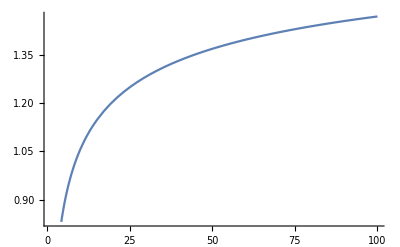

```mathematica
Plot[2-1.6788596711945776/W^(1/4), {W, 1, 100}]
```

```mathematica
allom
```

{μ1[W]→1.67886/W^(1/4),K1[W]→0.317265/W^(3/4),μ2[W]→1.67886/(f W)^(1/4),K2[W]→0.317265/(f W)^(3/4)}

```mathematica
InvFitW/.allom
(* This must be positive for persistence of the resident *)
(β K1[W] (λ-μ1[W]))/(γ μ1[W])/.allom
```

{μ1[W]→1.67886/W^(1/4),K1[W]→0.317265/W^(3/4),μ2[W]→1.67886/(f W)^(1/4),K2[W]→0.317265/(f W)^(3/4)}

r

(0.188977 β (-1.67886/W^(1/4)+λ))/(√W γ)